General::obspkg: "VectorFieldPlots`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

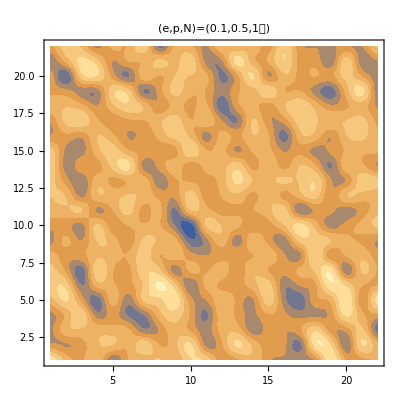

-Graphics3D-

```mathematica
Needs["VectorFieldPlots`"];
SetDirectory[NotebookDirectory[]];
p=ReadList["thetaB0T1.txt",Number,RecordLists-> True];
q=ReadList["phiB0T1.txt",Number,RecordLists-> True];
L=24;
p2=Table[{Sin[p[[1,L*(i-1)+j]]]*Cos[q[[1,L*(i-1)+j]]],Sin[p[[1,L*(i-1)+j]]]*Sin[q[[1,L*(i-1)+j]]],Cos[p[[1,L*(i-1)+j]]]},{i,1,L,1},{j,1,L,1}];
edge=1;
chirality=Table[p2[[i,j]].(
     Cross[p2[[i+1,j]],p2[[i,j+1]]]
+Cross[p2[[i-1,j+1]],p2[[i-1,j]]]
+Cross[p2[[i,j+1]],p2[[i,j-1]]]
+Cross[p2[[i-1,j]],p2[[i-1,j-1]]]
+Cross[p2[[i,j-1]],p2[[i+1,j-1]]]
+Cross[p2[[i+1,j+1]],p2[[i,j+1]]]
+Cross[p2[[i-1,j+1]],p2[[i-1,j]]]
+Cross[p2[[i-1,j-1]],p2[[i,j-1]]]
+Cross[p2[[i+1,j-1]],p2[[i+1,j]]]),{i,1+edge,L-edge},{j,1+edge,L-edge}];
ListContourPlot[chirality,PlotLabel->Style["(e,p,N)=(0.1,0.5,1만)",FontSize->20],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ContourStyle->None,InterpolationOrder->2]

coord =Flatten[Table[{x,y},{x,1,L,1},{y,1,L,1}],1];
CONFnewlist=Table[{{coord[[i]][[1]],coord[[i]][[2]],0},Flatten[p2,1][[i]]},{i,L*L}];
ListVectorFieldPlot3D[CONFnewlist,ScaleFactor->1,VectorHeads->True]
```